Eliminate::ifun: Eliminate 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

(-g m^2 v0 Log[-(m v0 Cos[(π θ0)/180])/(b x-m v0 Cos[(π θ0)/180])]+b g m x Sec[(π θ0)/180]+b^2 v0 x Tan[(π θ0)/180])/(b^2 v0)

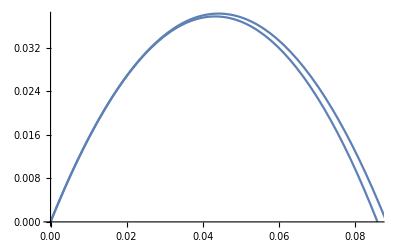

```mathematica
ClearAll["Global`*"]
sol=DSolve[{x''[t]==-b/m*x'[t],y''[t]==-b/m*y'[t]-g,y[0]==0,x[0]==0,y'[0]==v0*Sin[θ0*Pi/180],x'[0]==v0*Cos[θ0*Pi/180]},{x[t],y[t]},t];
x[t_]=x[t]/.Flatten[sol][[1]];
y[t_]=y[t]/.Flatten[sol][[2]];
path=Solve[Eliminate[{x==x[t],y==y[t]},t],y];
y[x_]=y/.Flatten[path][[1]];
y[x]
ClearAll["Global`*"]
project[v0_/;v0>0]:=Module[
{m=0.14,b=0.033,g=9.8,θ0=60,vx0,vy0,x,xmax,s1,s2,H,R},
vx0=Cos[θ0*Pi/180];
vy0=Sin[θ0*Pi/180];
H=vy0^2/(2*g);
R=2*vx0*vy0/g;
xmax=NSolve[{b*g*m*x+b^2* vy0* x-g*m^2* vx0 *Log[(m *vx0)/(m *vx0-b*x)]==0&&0<x<R},x];
xmax=x/.Flatten[xmax][[1]];
s1=
Plot[(b g m x+b^2 vy0 x-g m^2 vx0 Log[(m vx0)/(m vx0-b x)])/(b^2 vx0),{x,0,xmax}];
s2=
Plot[vy0/vx0*x-0.5*g*x^2/vx0^2,{x,0,R}];
Show[s1,s2]
]
project[45]
```